## White noise (random number generator)

```mathematica
nn=10000;
t=Table[RandomReal[{0,1}],{i,1,nn}];
Print[t[[1;;10]]]
```

{0.825154,0.808134,0.465484,0.832199,0.598512,0.496031,0.384,0.545148,0.559249,0.0843403}

number of steps 10000

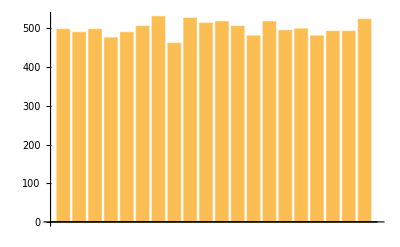

```mathematica
d=BinCounts[t,0.05];
Print[" number of steps ",Plus@@d]
BarChart[d]
```

```mathematica
Manipulate[BarChart[BinCounts[Table[RandomReal[],{i,1,a}],0.05]],{a,10,100000,50}]
```

## PDF vs. CDF

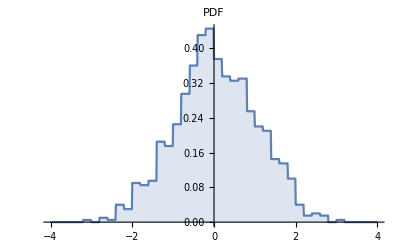
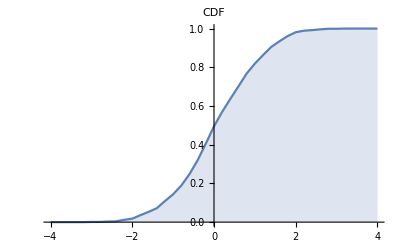

```mathematica
data=RandomVariate[NormalDistribution[0,1],10^3];(* 0 is mean, 1 is standard deviation. Change the power of the 10 from 1 to 5 *)
𝒟=HistogramDistribution[data];
DiscretePlot[#[𝒟,x],{x,-4,4,.01},PlotLabel->#]&/@{PDF,CDF}
```

## Accumulating Random shots PDF vs. Histogram

Accumulating random numbers in the interval [0,1]

		X = 1/N ∑_i  x_i

```mathematica
accum[n_]:=Sum[RandomReal[{0,1}],{i,1,n}]/n
nn=10000;nCap=1000; (* nCap = N *)
a=Table[accum[nCap],{i,nn}]; (* Calling accum function nn times to each time get the average of nCap samples *)
Print[a[[1;;10]]]
d=HistogramDistribution[a];
```

{0.487363,0.516486,0.5032,0.49565,0.492416,0.506947,0.501428,0.485392,0.497585,0.525889}

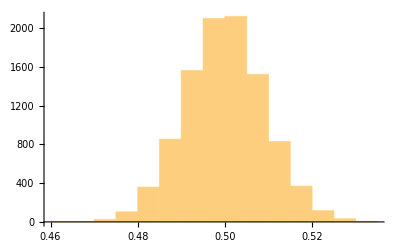

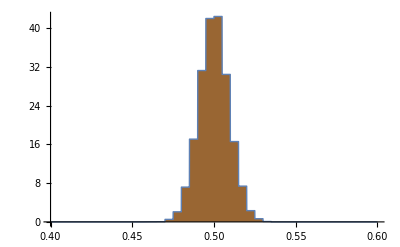

```mathematica
Histogram[a]
gr1=Plot[PDF[d,x],{x,0.4,0.6},PlotStyle->Thick,Filling->Axis,FillingStyle->Brown,PlotRange->All]
```

The distribution of single shots is constant, p(x)=1, but the distribution of accumulated events X is Gaussian.

## Variance of X

```mathematica
Print[" mean of X ",Mean[a]]
Print[" variance of X = ",σ2=Variance[a]," <X^2>*N = ",σ2*nCap]
```

mean of X 0.499998

variance of X = 0.0000826851 <X^2>*N = 0.0826851

## Distribution functions of statistics

### Gaussian distribution function

The probability density of the Gaussian distribution is given by the equation
			
			p(X) =1/√(2π σ^2)exp[- (X-<X>)^2/(2 σ^2)]

(ⅇ^(-(x-xav)^2/(2 σ^2)))/(√(2 π) √(σ^2))

General::munfl: Exp[-1511.64] is too small to represent as a normalized machine number; precision may be lost.

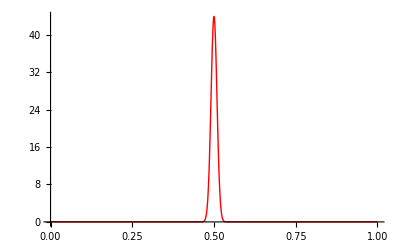

```mathematica
Clear[x,σ,xav]
p[x_,σ_,xav_]=1/Sqrt[2π*σ^2]*Exp[-(x-xav)^2/(2σ^2)]
gr2=Plot[p[x,Sqrt[σ2],0.5],{x,0,1},PlotStyle->{Red,Thick},PlotRange->All]
(*gr3=Plot[p[x,Sqrt[σ2],0.5],{x,0.4,0.6},PlotStyle->{Red,Thick},PlotRange->All]*)
```

### Compare the results

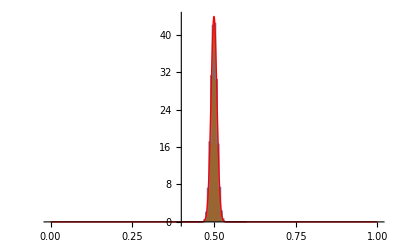

```mathematica
(*Show[gr1,gr3]*)
Show[gr1,gr2]
```

## Normalization, average, and variance

Normalization, mean, and variance of a Gaussian process

```mathematica
Print[" normalization     = ",Integrate[p[x,σ,xav],{x,-∞,∞},Assumptions->σ>0]]
Print[" mean              = ",Integrate[x*p[x,σ,xav],{x,-∞,∞},Assumptions->σ>0]]
Print[" variance          = ",Integrate[(x-xav)^2*p[x,σ,xav],{x,-∞,∞},Assumptions->σ>0]]
```

normalization     = 1

mean              = xav

variance          = σ^2